```mathematica
sol = DSolve[y'[x] + y Tan[x] == Sin[2x], y, x]
```

DSolve::dvnoarg: The function y appears with no arguments.

```mathematica
DSolve[y [x]Tan[x]+y'[x]==Sin[2 x],y,x]
```

{{y→Function[{x},C[1] Cos[x]-2 Cos[x]^2]}}

```mathematica
DSolve[{y [x]Tan[x]+y'[x]==Sin[2 x], y[0] == 2},y,x]
```

{{y→Function[{x},-2 (-2 Cos[x]+Cos[x]^2)]}}

```mathematica
y[x] /. First[DSolve[{y [x]Tan[x]+y'[x]==Sin[2 x], y[0] == 2},y,x]]
```

-2 (-2 Cos[x]+Cos[x]^2)

```mathematica
foo[x_] = y[x] /. First[DSolve[{y [x]Tan[x]+y'[x]==Sin[2 x], y[0] == 2},y,x]]
```

-2 (-2 Cos[x]+Cos[x]^2)

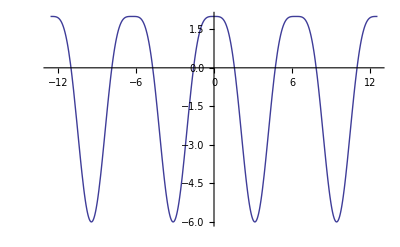

```mathematica
Plot[foo[x], {x, -4Pi, 4Pi}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
ndsol1 =NDSolve[{x''[t] + 4 x [t] == 0, x[0] == 1, x'[0] == 0}, x, {t,-2Pi,2Pi}]
```

{{x→InterpolatingFunction[{{-6.28319,6.28319}},<>]}}